```mathematica
v = {0.0,0.5,1.0,1.5,2.0,2.5,3.0,3.5,4.0,4.5,5.0,5.5,6.0,6.5,7.0,7.5,8.0,8.5,9.0,9.5,10.0,10.5,11.0,11.5,12.0,12.5,13.0,13.5,14.0,14.5,15.0,15.5,16.0};
c1 = {-0.0,-0.0,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.17,0.18,0.19,0.2,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33};
c2 ={-0.0,-0.0,-0.0,0.01,0.02,0.03,0.03,0.04,0.05,0.06,0.06,0.07,0.08,0.09,0.1,0.1,0.11,0.12,0.13,0.14,0.14,0.15,0.16,0.17,0.18,0.18,0.19,0.2,0.2,0.21,0.22,0.23,0.24};
c3 = {-0.0,-0.0,0.01,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28};
```

```mathematica
data1= Transpose[{v,c1}];
lm1 = LinearModelFit[data1,x,x]
data2 = Transpose[{v,c2}];
lm2 = LinearModelFit[data2,x,x]
data3 = Transpose[{v,c3}];
lm3 = LinearModelFit[data3,x,x]
```

FittedModel[-0.0143672+0.0216444 x]

FittedModel[-0.0113191+0.0154679 x]

FittedModel[-0.0115865+0.0180013 x]

```mathematica
Normal[lm3]
```

```mathematica
(0.021644385026737985+0.015467914438502645+0.01800133689839572)/3
```

0.0183712

```mathematica
Normal[lm2]
```

-0.0113191+0.0154679 x

```mathematica
Normal[lm3]
```

-0.0115865+0.0180013 x

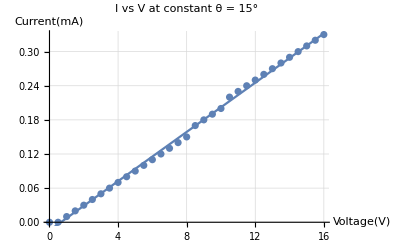

```mathematica
Show[ListPlot[data1, AxesLabel->{"Voltage(V)", "Current(mA)"}],Plot[lm1[x],{x,0,16}], PlotLabel->"I vs V at constant θ = 15° ", GridLines->Automatic]
```

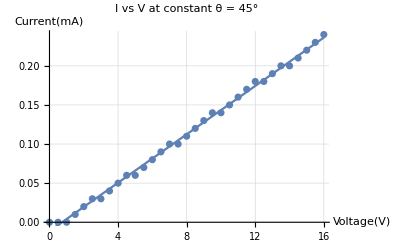

```mathematica
Show[ListPlot[data2, AxesLabel->{"Voltage(V)", "Current(mA)"}],Plot[lm2[x],{x,0,16}], PlotLabel->"I vs V at constant θ = 45° ", GridLines->Automatic]
```

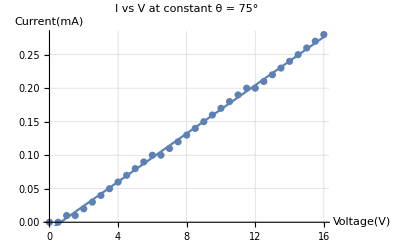

```mathematica
Show[ListPlot[data3, AxesLabel->{"Voltage(V)", "Current(mA)"}],Plot[lm3[x],{x,0,16}], PlotLabel->"I vs V at constant θ = 75° ", GridLines->Automatic]
```

```mathematica
θ = Range[0,180,10];
c1 = {-0.1,-0.08,-0.07,-0.05,-0.04,-0.02,-0.01,-0.01,-0.01,-0.01,-0.02,-0.03,-0.04,-0.05,-0.06,-0.07,-0.07,-0.07,-0.06}(-1);
c2 = {-0.1,-0.08,-0.07,-0.05,-0.03,-0.02,-0.02,-0.02,-0.04,-0.05,-0.06,-0.08,-0.1,-0.11,-0.13,-0.15,-0.16,-0.15,-0.13}(-1);
c3 = {-0.16,-0.13,-0.11,-0.09,-0.09,-0.09,-0.08,-0.08,-0.11,-0.13,-0.17,-0.22,-0.26,-0.3,-0.35,-0.39,-0.4,-0.39,-0.36}(-1);
```

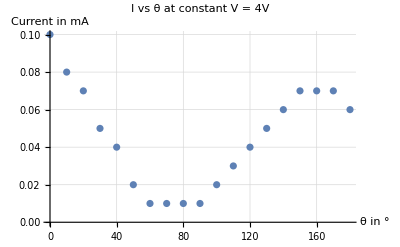

```mathematica
ListPlot[Transpose[{θ,c1}], Joined->False, AxesLabel->{"θ in °", "Current in mA"}, PlotLabel->"I vs θ at constant V = 4V", GridLines->Automatic]
```

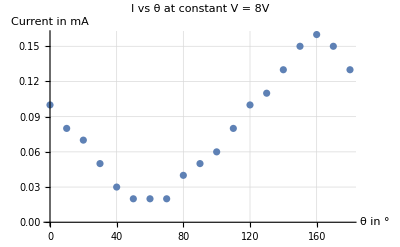

```mathematica
ListPlot[Transpose[{θ,c2}], Joined->False, AxesLabel->{"θ in °", "Current in mA"}, PlotLabel->"I vs θ at constant V = 8V", GridLines->Automatic]
```

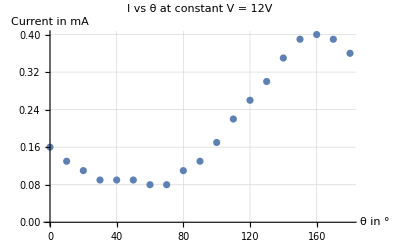

```mathematica
ListPlot[Transpose[{θ,c3}], Joined->False, AxesLabel->{"θ in °", "Current in mA"}, PlotLabel->"I vs θ at constant V = 12V", GridLines->Automatic]
```